```mathematica
probIApp[{xM,yM,phiM},{x,y},R,sx,sl]
```

ⅇ^(-(sl^2 x^2-2 sl^2 x xM+sl^2 xM^2+2 sx^2 y^2-4 sx^2 y yM+2 sx^2 yM^2-2 sl^2 x y Tan[phiM]+2 sl^2 xM y Tan[phiM]+2 sl^2 x yM Tan[phiM]-2 sl^2 xM yM Tan[phiM]+(sl^2+2 sx^2) (y-yM)^2 Tan[phiM]^2)/(sl^2 sx^2)+((2 sl^2 (-x+xM) y-2 sl^2 y (-y+yM) Tan[phiM]-4 sx^2 y (-y+yM) Tan[phiM]+2 sl^2 (-x+xM) y Tan[phiM]^2+2 (sl^2+2 sx^2) y (y-yM) Tan[phiM]^3)^2)/(4 sl^2 sx^2 (R^2 sl^2+y (sl^2 y+2 sx^2 (y-yM))-2 sl^2 x y Tan[phiM]+2 sl^2 xM y Tan[phiM]+2 (R^2 sl^2+y (sx^2 (4 y-3 yM)+sl^2 (2 y-yM))) Tan[phiM]^2-2 sl^2 (x-xM) y Tan[phiM]^3+(R^2 sl^2+(sl^2+2 sx^2) y (3 y-2 yM)) Tan[phiM]^4)))/(2 √2 π sl sx^2 √(1/(sl^2 sx^2)(R^2 sl^2+y (sl^2 y+2 sx^2 (y-yM))-2 sl^2 x y Tan[phiM]+2 sl^2 xM y Tan[phiM]+2 (R^2 sl^2+y (sx^2 (4 y-3 yM)+sl^2 (2 y-yM))) Tan[phiM]^2-2 sl^2 (x-xM) y Tan[phiM]^3+(R^2 sl^2+(sl^2+2 sx^2) y (3 y-2 yM)) Tan[phiM]^4)))

```mathematica
f[{xM_,yM_,phiM_},{x_,y_},R_,sx_,sl_]=(2 √2 π sl sx^2 √(1/(sl^2 sx^2)(R^2 sl^2+y (sl^2 y+2 sx^2 (y-yM))-2 sl^2 x y Tan[phiM]+2 sl^2 xM y Tan[phiM]+2 (R^2 sl^2+y (sx^2 (4 y-3 yM)+sl^2 (2 y-yM))) Tan[phiM]^2-2 sl^2 (x-xM) y Tan[phiM]^3+(R^2 sl^2+(sl^2+2 sx^2) y (3 y-2 yM)) Tan[phiM]^4)))
```

2 √2 π sl sx^2 √(1/(sl^2 sx^2)(R^2 sl^2+y (sl^2 y+2 sx^2 (y-yM))-2 sl^2 x y Tan[phiM]+2 sl^2 xM y Tan[phiM]+2 (R^2 sl^2+y (sx^2 (4 y-3 yM)+sl^2 (2 y-yM))) Tan[phiM]^2-2 sl^2 (x-xM) y Tan[phiM]^3+(R^2 sl^2+(sl^2+2 sx^2) y (3 y-2 yM)) Tan[phiM]^4))

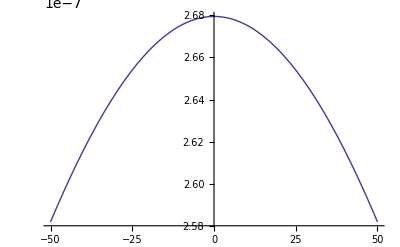

```mathematica
Plot[1/f[{0,0,Pi/4},{0,y},350,20,30],{y,-50,50}]
```

```mathematica
1/f[{xM,yM,0},{x,y},350,20,30]
```

1/(40 √2 π √(110250000+y (900 y+800 (y-yM))))

```mathematica
%//Simplify
```

1/(400 π √(2205000+34 y^2-16 y yM))

```mathematica
%/.y->yM+dy
```

1/(400 π √(2205000-16 yM (dy+yM)+34 (dy+yM)^2))

```mathematica
%//Simplify
```

1/(400 π √(2205000-16 yM (dy+yM)+34 (dy+yM)^2))

```mathematica
%+O[dy]^3
```

1/(400 π √(2205000+18 yM^2))-(13 yM dy)/(200 (π (2205000+18 yM^2)^(3/2)))+((-3123750+59 yM^2) dy^2)/(32400 √2 π (122500+yM^2)^(5/2))+O[dy]^3

```mathematica
%//Simplify
```

1/(400 π √(2205000+18 yM^2))-(13 yM dy)/(200 (π (2205000+18 yM^2)^(3/2)))+((-3123750+59 yM^2) dy^2)/(32400 √2 π (122500+yM^2)^(5/2))+O[dy]^3

```mathematica
%51/.yM->35.0
```

5.33243×10^-7-2.1789×10^-10 dy-3.93692×10^-12 dy^2+O[dy]^3